```mathematica
polycali=LinguisticAssistant["Polygon"];
polycali=polycali[[1,1]];
polycali=Map[Map[Reverse,#]&,polycali];
polycali=Map[Map[{360+#[[1]],#[[2]]}&,#]&,polycali];
```

```mathematica
x1=GeoGraphics[{FaceForm[],Polygon[{{120,-40},{120,60},{270,60},{270,-40}}],FaceForm[Red],Polygon[polycali]}]
```

## NINO

```mathematica
nino12=Polygon[{{270,-10},{270,0},{280,0},{280,-10}}];
nino3=Polygon[{{210,-5},{210,5},{270,5},{270,-5}}];
nino34=Polygon[{{190,-5},{190,5},{240,5},{240,-5}}];
nino4=Polygon[{{160,-5},{160,5},{210,5},{210,-5}}];
pacific=Polygon[{{120,-40},{120,60},{280,60},{280,-40}}];
```

```mathematica
x1=GeoGraphics[{FaceForm[],pacific,
			    FaceForm[Red],Polygon[polycali],
			    FaceForm[Green],nino12,
    			FaceForm[Blue],nino3,
                                FaceForm[],EdgeForm[Thick],nino34,
                                FaceForm[Yellow],EdgeForm[],nino4}]
```

-Graphics-

## SOI

```mathematica
darwin=GeoPosition[LinguisticAssistant];
darwin=darwin[[1]];
darwin=Reverse[darwin];
tahiti=GeoPosition[LinguisticAssistant];
tahiti=tahiti[[1]];
tahiti={360+tahiti[[2]],tahiti[[1]]};
```

```mathematica
GeoGraphics[Line[{darwin,tahiti}]]
```

-Graphics-

```mathematica
x2=GeoGraphics[{FaceForm[],pacific,
			    FaceForm[Red],Polygon[polycali],
			    FaceForm[Green],nino12,
    			FaceForm[Blue],nino3,
                                FaceForm[],EdgeForm[Thick],nino34,
                                FaceForm[Yellow],EdgeForm[],nino4,
			     {Dashed,Line[{darwin,tahiti}]},
		             {PointSize[0.02],Point[darwin]},
			    {PointSize[0.02],Point[tahiti]}}]
```

## Pacific Decadal Oscillation

The Pacific Decadal Oscillation (PDO) Index is defined as the leading principal component of North Pacific monthly sea surface temperature variability.

```mathematica
pacificpoly=LinguisticAssistant["Polygon"];
pacificpoly=pacificpoly[[1,1]];
pacificpoly=Map[Map[Reverse,#]&,pacificpoly];
pacificpoly[[1]]=Map[{360+#[[1]],#[[2]]}&,pacificpoly[[1]]];
Graphics[Polygon[pacificpoly]];
pacificpoly[[2]];
GeoGraphics[Polygon[pacificpoly]]
GeoGraphics[Polygon[pacificpoly[[1]]]]
GeoGraphics[Polygon[pacificpoly[[2]]]]
```

-Graphics-

-Graphics-

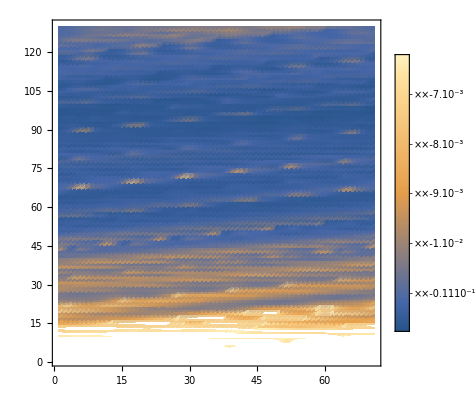

```mathematica
p1=Import["/Users/penn/Documents/Code/Github/PhDThesis/data/SST/Principal_1.mat","Table"];
p1=ArrayReshape[p1,{130,71}];
ListDensityPlot[Reverse@p1,PlotLegends -> Automatic]
```

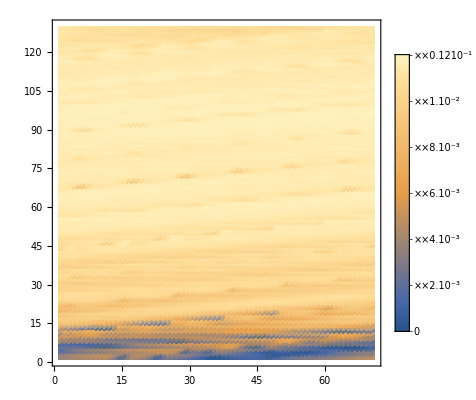

```mathematica
ListDensityPlot[Reverse@(Abs[p1]),PlotRange->All,PlotLegends -> Automatic]
```

```mathematica
ListDensityPlot[Reverse@(1000*p1),PlotRange->All,PlotLegends -> Automatic]
```

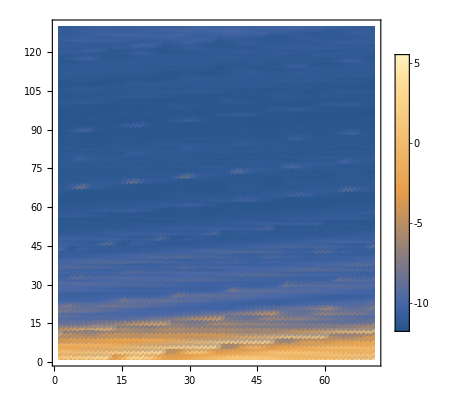

## Pacific-North American

The PNA index is obtained by projecting the PNA loading pattern to the daily anomaly 500 millibar height field over 0-90°N. The PNA loading pattern has been chosen as the second mode of a Rotated EOF analysis using monthly mean 500 millibar height anomaly data from 1950 to 2000 over 0-90°N latitude.